```mathematica
МЕТОД ГЛАВНЫХ КОМПОНЕНТ

ПРИМЕР 1.
```

МЕТОД ГЛАВНЫХ КОМПОНЕНТ

1. ПРИМЕР

Латентные переменные. Измерить неизмеримое.
  Например, качество жизни.

#### Исходные данные

Изучается средняя продолжительность жизни (L) в 1970-1998 годах, а также ряд других признаков: количество чиновников (M), количество автомобилей (A), доходы бедных (P), объемы продажи водки (V). Необходимо отразить качество жизни в различные годы с помощью меньшего количества признаков.

-Graphics-

-Graphics-

Исходные данные   Xi - вектор
i=7  количество объектов,  k=5 количество переменных

```mathematica
d={{68.9,1060 ,7.8,5.5,  25.3},{68.1,1101,9.5,15.3,28},{67.6,1147,10.1,30.2,30},{69.2,1204,10.0,44.5,23.50},
{69.2,1602,9.8,58.6,18},{64.6,1893,5.5,93.3,38.4},
{67.0,2777,6.2,122.0,29.6}};
%//MatrixForm;
god={1970,1975,1980,1985,1990,1995,1998};
```

```mathematica
Grid[Prepend[MapThread[Prepend,{d,god}],{"","L","M","P","A","V"}],Frame->All,Background->{None,{Yellow}}]
```

| L | M | P | A | V
1970 | 68.9 | 1060 | 7.8 | 5.5 | 25.3
1975 | 68.1 | 1101 | 9.5 | 15.3 | 28
1980 | 67.6 | 1147 | 10.1 | 30.2 | 30
1985 | 69.2 | 1204 | 10. | 44.5 | 23.5
1990 | 69.2 | 1602 | 9.8 | 58.6 | 18
1995 | 64.6 | 1893 | 5.5 | 93.3 | 38.4
1998 | 67. | 2777 | 6.2 | 122. | 29.6

1).  Алгоритм 1.  Метод Главных Компонент. Решение вручную.

В первую очередь необходимо провести стандартизацию
z-стандартизация:  данные центрируются (среднее=0) и нормируются (дисперсия=1).

```mathematica
Grid[dz=Standardize@d//N,Frame->All]
dz
{Mean[%]//Chop,Variance[%]}
```

0.670682 | -0.768041 | -0.319147 | -1.12014 | -0.354039
0.182913 | -0.702515 | 0.564073 | -0.887921 | 0.0721609
-0.121942 | -0.628999 | 0.875798 | -0.534851 | 0.387865
0.853595 | -0.537902 | 0.823844 | -0.195999 | -0.638173
0.853595 | 0.098174 | 0.719935 | 0.138113 | -1.50636
-1.95107 | 0.563245 | -1.51409 | 0.960362 | 1.71382
-0.487769 | 1.97604 | -1.15041 | 1.64044 | 0.324724

{{0.670682,-0.768041,-0.319147,-1.12014,-0.354039},{0.182913,-0.702515,0.564073,-0.887921,0.0721609},{-0.121942,-0.628999,0.875798,-0.534851,0.387865},{0.853595,-0.537902,0.823844,-0.195999,-0.638173},{0.853595,0.098174,0.719935,0.138113,-1.50636},{-1.95107,0.563245,-1.51409,0.960362,1.71382},{-0.487769,1.97604,-1.15041,1.64044,0.324724}}

{{0,0,0,0,0},{1.,1.,1.,1.,1.}}

```mathematica
Variance[dz]//Total  (* Общая дисперсия  *)
```

5.

Построим корреляционную матрицу

```mathematica
cor=Correlation[dz];
%//MatrixForm
```

(1. | -0.50084 | 0.769223 | -0.595292 | -0.934048
-0.50084 | 1. | -0.700093 | 0.953664 | 0.296602
0.769223 | -0.700093 | 1. | -0.66918 | -0.680883
-0.595292 | 0.953664 | -0.66918 | 1. | 0.37011
-0.934048 | 0.296602 | -0.680883 | 0.37011 | 1.)

ДОПОЛНИТЕЛЬНО.   Применять РСА? 

1) Проверить графически.
Визуализировать корреляционную матрицу. Диаграмма рассеяния.

2)
Тест сферичности Бартлетта
Индекс KMO 

ВЫВОДЫ сформулировать.

Найдем собственные числа (СЧ) и собственные векторы (СВ) корреляционной матрицы.

Замечание1: функция Eigenvectors  помещает СВ по строкам. 
Замечание2: Так как исходные данные Z-стандартизированы, 
корреляционная матрица = ковариационной матрице
Замечание3: Так как корреляционная матрица вещественная и симметричная, то ее собственные значения вещественны.
Замечание4: Корреляционная матрица - неотрицательно определённая матрица. Обычно, на практике,  корреляционная матрица положительно определенна, все ее собственные числа больше нуля.
Замечание 5: Собственные векторы, отвечающие различным собственным числам, ортогональны.

```mathematica
dval=Eigenvalues[cor]
(dvec=Eigenvectors[cor])//MatrixForm(* Собственные векторы - по строкам *)
```

{3.60001,1.08999,0.244925,0.0465064,0.0185715}

(0.472291 | -0.42956 | 0.476894 | -0.446385 | -0.407102
-0.381124 | -0.539835 | -0.0428492 | -0.46524 | 0.5874
-0.297042 | 0.0326039 | 0.851618 | 0.380852 | 0.201004
-0.499048 | -0.538495 | -0.167028 | 0.330656 | -0.568984
0.542589 | -0.482717 | -0.132609 | 0.574379 | 0.353673)

```mathematica
Total[Variance[dz]]
Total[dval]  (* Общая дисперсия не изменилась  *)
```

5.

5.

Матрица собственных векторов является матрицей перехода:  Y = CB*X

Главные компоненты - новые переменные

Утверждение. Направление максимальной дисперсии у проекции совпадает с собственным вектором, имеющим максимальное собственное значение, равное величине этой дисперсии.
И это справедливо также для проекций на большее количество измерений – дисперсия (ковариационная матрица) проекции на m-мерное пространство будет максимальна в направлении m собственных векторов, имеющих максимальные собственные значения.

Найдем Главные компоненты.

```mathematica
pc1=dz.Transpose[dvec]
```

{{1.13862,0.485849,-0.993823,-0.0367486,0.00837424},{1.02414,0.740843,0.0794753,-0.141853,-0.12092},{0.711112,0.825169,0.635822,-0.144256,-0.0487047},{1.37439,-0.353924,0.227587,0.024369,0.275275},{1.2559,-1.35826,0.112574,0.303661,-0.133138},{-3.01187,1.06432,0.0187283,0.265685,0.0280064},{-2.49228,-1.40399,-0.0803633,-0.270858,-0.00889301}}

Найдем Главные компоненты. Факторы - нормированные главные компоненты.
Делим на корень из соответствующего собственного значения.

```mathematica
pcn1=Table[pc1[[i]]/Sqrt[dval],{i,1,Dimensions[dz][[1]]}];
%//MatrixForm
```

(0.600105 | 0.465362 | -2.00813 | -0.170406 | 0.06145
0.539769 | 0.709603 | 0.160589 | -0.65778 | -0.887305
0.374788 | 0.790374 | 1.28475 | -0.668925 | -0.357394
0.724363 | -0.339 | 0.459865 | 0.113001 | 2.01996
0.661915 | -1.30099 | 0.227469 | 1.4081 | -0.976963
-1.58739 | 1.01944 | 0.0378427 | 1.232 | 0.20551
-1.31355 | -1.34479 | -0.162383 | -1.25599 | -0.0652567)

Найдем Факторные нагрузки, корреляция между исходными данными и факторами

```mathematica
df1=Correlation[dz,pc1];
%//MatrixForm
```

(0.89611 | -0.397903 | -0.147006 | -0.107621 | 0.0739427
-0.815034 | -0.563601 | 0.0161356 | -0.116128 | -0.0657835
0.904844 | -0.0447356 | 0.421464 | -0.0360203 | -0.0180717
-0.846958 | -0.485721 | 0.188483 | 0.0713071 | 0.0782748
-0.772424 | 0.613259 | 0.0994764 | -0.122703 | 0.0481976)

```mathematica
df1=Correlation[dz,pcn1];
%//MatrixForm
```

(0.89611 | -0.397903 | -0.147006 | -0.107621 | 0.0739427
-0.815034 | -0.563601 | 0.0161356 | -0.116128 | -0.0657835
0.904844 | -0.0447356 | 0.421464 | -0.0360203 | -0.0180717
-0.846958 | -0.485721 | 0.188483 | 0.0713071 | 0.0782748
-0.772424 | 0.613259 | 0.0994764 | -0.122703 | 0.0481976)

МЕТОДЫ ОПРЕДЕЛЕНИЯ МИНИМАЛЬНОГО КОЛИЧЕСТВА ФАКТОРОВ
Критерий, основанный на собственных числах.

Оставлять главные компоненты (факторы) с собственными  числами, большими 1 (используется корреляционная матрица). Дает нижнюю оценку числа общих факторов.

ДОПОЛНИТЕЛЬНО. Определите количество факторов.

МЕТОДЫ ОПРЕДЕЛЕНИЯ МИНИМАЛЬНОГО КОЛИЧЕСТВА ФАКТОРОВ
Графический критерий
Определение количества факторов графически
Критерий "Каменистой осыпи",критерий Кеттелла (Cattell,1966)
2-3 фактора
Графическое изображение собственных чисел корреляционной матрицы, которые наносятся на график в порядке убывания (Кеттелл). Выделение заканчивается на том факторе, после которого исследуемая зависимость близка к горизонтальной прямой линии.

ДОПОЛНИТЕЛЬНО. Определите количество факторов.

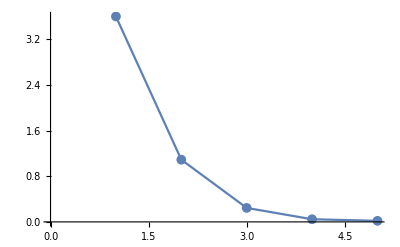

```mathematica
ListLinePlot[dval,PlotMarkers->{Automatic, 10}]
```

МЕТОДЫ ОПРЕДЕЛЕНИЯ МИНИМАЛЬНОГО КОЛИЧЕСТВА ФАКТОРОВ
% дисперсии переменной объясненной фактором  
Объясненная суммарная дисперсия

```mathematica
dval
```

{3.60001,1.08999,0.244925,0.0465064,0.0185715}

```mathematica
dval/Total[dval]*100
Accumulate[dval]/Total[dval]* 100
```

{72.0002,21.7997,4.8985,0.930128,0.37143}

{72.0002,93.7999,98.6984,99.6286,100.}

Первый фактор объясняет 72% суммарной дисперсии
Второй фактор объясняет 21.8 % суммарной дисперсии
Первый + Второй объясня.т 93.8 % суммарной дисперсии

| Ф1 | Ф2 | Ф3 | Ф4 | Ф5
L | 0.89611 | -0.397903 | -0.147006 | -0.107621 | 0.0739427
M | -0.815034 | -0.563601 | 0.0161356 | -0.116128 | -0.0657835
P | 0.904844 | -0.0447356 | 0.421464 | -0.0360203 | -0.0180717
A | -0.846958 | -0.485721 | 0.188483 | 0.0713071 | 0.0782748
V | -0.772424 | 0.613259 | 0.0994764 | -0.122703 | 0.0481976

```mathematica
Grid[Prepend[df1,{"Ф1","Ф2","Ф3","Ф4","Ф5"}],Frame->All,Background->{None,{Yellow}}]
```

Ф1 | Ф2 | Ф3 | Ф4 | Ф5
0.89611 | -0.397903 | -0.147006 | -0.107621 | 0.0739427
-0.815034 | -0.563601 | 0.0161356 | -0.116128 | -0.0657835
0.904844 | -0.0447356 | 0.421464 | -0.0360203 | -0.0180717
-0.846958 | -0.485721 | 0.188483 | 0.0713071 | 0.0782748
-0.772424 | 0.613259 | 0.0994764 | -0.122703 | 0.0481976

```mathematica
(* МАТРИЦА ФАКТОРНЫХ НАГРУЗОК  *)
```

С первым фактором сильно коррелируют все переменные 
(L+,M-,P+,A-,V-)
переменные M-,V+ относятся к двум факторам одновременно.
Первый фактор можно рассматривать, как признак благополучия.
Чем больше фактор, тем благополучнее год.

-Graphics-

Оставим два  фактора, для которых с.ч. > 1
Перейдем к факторам

```mathematica
pcn1[[1;;7,1;;2]]//Grid  (* факторы, новые переменные *)
```

0.600105 | 0.465362
0.539769 | 0.709603
0.374788 | 0.790374
0.724363 | -0.339
0.661915 | -1.30099
-1.58739 | 1.01944
-1.31355 | -1.34479

Признаки в пространстве двух факторов.

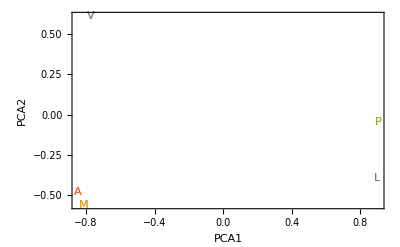

```mathematica
ListPlot[Table[{{df1[[i,1]],df1[[i,2]]}},{i,1,5}],Frame->True,FrameLabel->{"PCA1","PCA2"},PlotStyle->{Thick},PlotMarkers->{"L","M","P","A","V"}]
```

ДОПОЛНИТЕЛЬНО.

Дать интерпретацию полученному результату.

Признаки в пространстве двух факторов.   Видно, что признаки M и А сильно коррелируют между собой. Заметная корреляция есть и между признаками P и L. Признак V ни с кем не коррелирует. Таким образом, вместо 5 можно рассматривать три признака P-L, A-M, V. 
  Фактор РСА1 делит исходную совокупность на две части по признакам A-M  и P-L. 
  Этот фактор можно рассматривать, как признак благополучия. Чем больше фактор, тем благополучнее год.
  Фактор РСА2 трактовать труднее.

-Graphics-

Исходные данные (объекты)  в пространстве двух факторов.

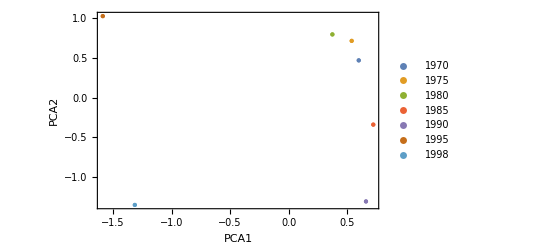

```mathematica
g=god//ToString;
ListPlot[Table[{{pcn1[[i,1]],pcn1[[i,2]]}},{i,1,7}],Frame->True,PlotLegends->god,FrameLabel->{"PCA1","PCA2"},PlotStyle->{PointSize[Large]}]
```

ДОПОЛНИТЕЛЬНО.

Дать интерпретацию полученному результату.

```mathematica
Grid[Prepend[MapThread[Prepend,{d,god}],{"","L","M","P","A","V"}],Frame->All,Background->{None,{Yellow}}]
```

| L | M | P | A | V
1970 | 68.9 | 1060 | 7.8 | 5.5 | 25.3
1975 | 68.1 | 1101 | 9.5 | 15.3 | 28
1980 | 67.6 | 1147 | 10.1 | 30.2 | 30
1985 | 69.2 | 1204 | 10. | 44.5 | 23.5
1990 | 69.2 | 1602 | 9.8 | 58.6 | 18
1995 | 64.6 | 1893 | 5.5 | 93.3 | 38.4
1998 | 67. | 2777 | 6.2 | 122. | 29.6

Исходные данные (объекты)  в пространстве двух факторов.
Можно сказать, чем больше первый фактор, тем лучше год.

Однако, НАМОМНИМ, что этот вывод не более чем гипотеза. 
Цель метода главных компонент - сокращение числа переменных! Можно выделить количество факторов, сформулировать гипотезы.
В результате получаем первичное факторное решение, которое не позволяет производить интерпретацию факторной структуры. Это связано с тем, что на первый фактор имеет большую нагрузку, по сравнению с остальными.
Для выяснения факторной структуры нужно проводить дополнительные исследования. 

При этом метод РСА активно используется на первом этапе в задачах с большим количеством переменных.

ДОПОЛНИТЕЛЬНО.

Дать графическую иллюстрацию, используя Biplot.

Дать интерпретацию полученному результату.

2)  Алгоритм 2. Метод главных компонент, с использованием функции  PrincipalComponents
pc2 -  Главные компоненты.
Соответствующие команды есть в R, например princomp.

```mathematica
pc2=T=PrincipalComponents[dz,Method->"Correlation"];
%//MatrixForm
```

(1.13862 | 0.485849 | 0.993823 | 0.0367486 | 0.00837424
1.02414 | 0.740843 | -0.0794753 | 0.141853 | -0.12092
0.711112 | 0.825169 | -0.635822 | 0.144256 | -0.0487047
1.37439 | -0.353924 | -0.227587 | -0.024369 | 0.275275
1.2559 | -1.35826 | -0.112574 | -0.303661 | -0.133138
-3.01187 | 1.06432 | -0.0187283 | -0.265685 | 0.0280064
-2.49228 | -1.40399 | 0.0803633 | 0.270858 | -0.00889301)

pcn2 - факторы - нормированные компоненты, используются при переходе от исходных переменных к факторам (новым переменным)

```mathematica
pcn2=Table[pc2[[i]]/Sqrt[dval],{i,1,Dimensions[dz][[1]]}]
```

{{0.600105,0.465362,2.00813,0.170406,0.06145},{0.539769,0.709603,-0.160589,0.65778,-0.887305},{0.374788,0.790374,-1.28475,0.668925,-0.357394},{0.724363,-0.339,-0.459865,-0.113001,2.01996},{0.661915,-1.30099,-0.227469,-1.4081,-0.976963},{-1.58739,1.01944,-0.0378427,-1.232,0.20551},{-1.31355,-1.34479,0.162383,1.25599,-0.0652567}}

Найдем Факторные нагрузки, корреляция между исходными данными и факторами

```mathematica
df2=Correlation[d,pcn2];
%//MatrixForm
```

(0.89611 | -0.397903 | 0.147006 | 0.107621 | 0.0739427
-0.815034 | -0.563601 | -0.0161356 | 0.116128 | -0.0657835
0.904844 | -0.0447356 | -0.421464 | 0.0360203 | -0.0180717
-0.846958 | -0.485721 | -0.188483 | -0.0713071 | 0.0782748
-0.772424 | 0.613259 | -0.0994764 | 0.122703 | 0.0481976)

3).  Алгоритм 3. СИНГУЛЯРНОЕ РАЗЛОЖЕНИЕ

Факторные нагрузки  и факторы  (матрицу новых переменных)
 можно найти используя матрицу сингулярных разложений SVD   

Обозначим их  P1 и Т1.

Здесь dz  - стандартизированные значения исходной матрицы Х

```mathematica
{u,w,v}=SingularValueDecomposition[dz]; (* отличается знаком от PCA - PrincipalComponents *)
```

```mathematica
T1=u.w;  (*  см. Т для РСА, главные компоненты (новые переменные) *)
T1//MatrixForm
```

(-1.13862 | 0.485849 | 0.993823 | -0.0367486 | -0.00837424
-1.02414 | 0.740843 | -0.0794753 | -0.141853 | 0.12092
-0.711112 | 0.825169 | -0.635822 | -0.144256 | 0.0487047
-1.37439 | -0.353924 | -0.227587 | 0.024369 | -0.275275
-1.2559 | -1.35826 | -0.112574 | 0.303661 | 0.133138
3.01187 | 1.06432 | -0.0187283 | 0.265685 | -0.0280064
2.49228 | -1.40399 | 0.0803633 | -0.270858 | 0.00889301)

```mathematica
T//MatrixForm (* для сравнения, некоторые столбцы отличаются знаком  *)
```

(1.13862 | 0.485849 | 0.993823 | 0.0367486 | 0.00837424
1.02414 | 0.740843 | -0.0794753 | 0.141853 | -0.12092
0.711112 | 0.825169 | -0.635822 | 0.144256 | -0.0487047
1.37439 | -0.353924 | -0.227587 | -0.024369 | 0.275275
1.2559 | -1.35826 | -0.112574 | -0.303661 | -0.133138
-3.01187 | 1.06432 | -0.0187283 | -0.265685 | 0.0280064
-2.49228 | -1.40399 | 0.0803633 | 0.270858 | -0.00889301)

```mathematica
P1=v;   (* собственные векторы *)
%//MatrixForm
```

(-0.472291 | -0.381124 | 0.297042 | -0.499048 | -0.542589
0.42956 | -0.539835 | -0.0326039 | -0.538495 | 0.482717
-0.476894 | -0.0428492 | -0.851618 | -0.167028 | 0.132609
0.446385 | -0.46524 | -0.380852 | 0.330656 | -0.574379
0.407102 | 0.5874 | -0.201004 | -0.568984 | -0.353673)

```mathematica
dvec//MatrixForm   (* для сравнения, по строкам  *)
```

(0.472291 | -0.42956 | 0.476894 | -0.446385 | -0.407102
-0.381124 | -0.539835 | -0.0428492 | -0.46524 | 0.5874
-0.297042 | 0.0326039 | 0.851618 | 0.380852 | 0.201004
-0.499048 | -0.538495 | -0.167028 | 0.330656 | -0.568984
0.542589 | -0.482717 | -0.132609 | 0.574379 | 0.353673)

ДОПОЛНИТЕЛЬНО.

Найти главные компоненты, 
Создать функцию, принимающую на входе матрицу исходных данных, дающую на выходе матрицу факторов. Решить задачу как k последовательных оптимизационных задач.

-Graphics-